### Wprowadzenie wartosci dla kata okreslajacego nachylenie wektora predkosci poczatkowej rakiety do poziomu ( "α" ), masy rakiety ( "m" ) i przyspieszenia ziemskiego ( "g" ).

```mathematica
ClearAll["Global`*"];
```

```mathematica
α=45;             (* deg *)
```

```mathematica
g=9.81;         (* m/s^2 *)
```

### Obliczenie skladowej poziomej wektora predkosci poczatkowej ( "v_x" ). Symbol "v_o" oznacza szybkosc poczatkowa rakiety.

```mathematica
vx=vo×cos(α °);
```

### Wprowadzenie wzorow na mase dwoch czlonow rakiety ( "m_1", "m_2" ).

```mathematica
m1=(1-x)×m;
m2=x×m;
```

### Wprowadzenie wzorow na ped rakiety przed rozlaczeniem ( "p_p" ) oraz na pedy dwoch czlonow rakiety powstajacych po jej rozlaczeniu ( "p_1", "p_2" ). Symbole "v_1" i "v_2" oznaczaja predkosci poszczegolnych fragmentow rakiety.

```mathematica
pp=m×vx;
p1=-m1×v1;
p2=m2×v2;
```

### Wykorzystanie zasady zachowania pedu do obliczenia predkosci czlonu rakiety, ktorego zasieg nalezy wyznaczyc ( "v_2" ).

```mathematica
A=Solve[{ p1+p2==pp,v1==vx},v2,v1];
```

Solve::bdomv: Warning: v1 is not a valid domain specification. Mathematica is assuming it is a variable to eliminate.

### Wprowadzenie wzorow na zasieg ( "z_uk" ) i maksymalna wysokosc ( "h_uk" ) ciala w rzucie ukosnym oraz na zasieg ciala w rzucie poziomym ( "z_poz" ).

```mathematica
zuk=(vo^2×sin(2×α °))/g;
huk=(vo^2×sin^2(α °))/(2×g);
zpoz=v2×√((2×huk)/g)/.A;
```

### Obliczenie zasiegu drugiego czlonu rakiety ( "s" ).

```mathematica
s=1/2×zuk+zpoz;
```

### Sporzadzenie wykresu obrazujacego zaleznosc zasiegu drugiego czlonu rakiety od szybkosci poczatkowej rakiety dla x = 0.2.

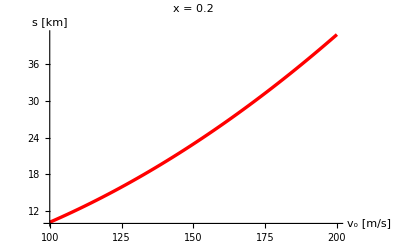

```mathematica
rys1=Plot[s×10^-3/.x->0.2,{vo,100,200},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     x = 0.2  ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v_o [m/s]","s [km] "}]
```

### Sporzadzenie wykresu obrazujacego zaleznosc zasiegu drugiego czlonu rakiety od szybkosci poczatkowej rakiety dla x = 0.4.

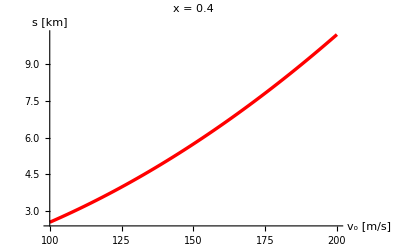

```mathematica
rys2=Plot[s×10^-3/.x->0.4,{vo,100,200},BaseStyle->{FontFamily->"Times",FontSlant->"Italic",FontSize->12},
PlotLabel->StyleForm["     x = 0.4  ",FontFamily->"Helvetica",FontSlant->"Plain",FontWeight->"Bold",FontSize->12],
PlotStyle->({{RGBColor[1,0,0], Thickness[0.006]}}),AxesLabel->{"v_o [m/s]","s [km] "}]
```

```mathematica
{{□}, {□}, {□}}
```

{{□},{□},{□}}